```mathematica
Impedance[α0_,χ0_,U0_,θ0_,η0_,P0_]:=
Module[{α=α0,U=U0,P,rule,X,L,n,smoothingFunc,v,V,max,vacuum,plasma,u,hg,υ,ϵ,g,system,R,RP,Dissipation},
(*α - dissipation, α==ν/ω, ω->ω(1+ⅈα);
χ - dimensionless wave vector magnitude; χ=Subscript[k, 0] L, and L==v'[Subscript[x, 0]]^-1 where v[Subscript[x, 0]]==0;
U - anizatropy: p^2==4πe^2*n/m, b==eB/(mc), v==p^2/ω^2, u==b^2/ω^2, and with dissipation: v->v(1-ⅈα), u->U(1-ⅈα);
θ - angel between wave vector and XOY;
η - angle between wave vector projection and density gradient direction;
P - wave polarisation in native mode (O-X); 2d-vector*)

(*=====================================================================================================================*)
(*Natural plasma parameters,without dimensionlesses*)
Subscript[X, 0]=3;Subscript[V, max]=2;(*plasma boundary and depth; it makes reflection point equal to -Subscript[X, 0] √(1-1/Subscript[V, max]) for U==0*)
n=0.1;(*smoothing width, in parts of plasma whight*)
υ=Function[x,Subscript[V, max](1-x^2/Subscript[X, 0]^2)(*(2 Subscript[V, max] √(1-1/Subscript[V, max])x/Subscript[X, 0])*)];smoothingFunc=Function[x,(1+(x/Subscript[X, 0])^(2/n))^-1];
v=Function[x,υ[x]smoothingFunc[x](1-ⅈ α)];u=U(1-ⅈ α);
(*=====================================================================================================================*)
L=υ'[hg/.NSolve[υ[hg]==1(*-U*)&&-Subscript[X, 0]<hg<0,hg]⟦1⟧]^-1;(*For dimensionless*)
ϵ=Function[x,1-v[x L]/(1-u)];Subscript[ϵ, l]=Function[x,1-v[x L]];g=Function[x,(√u)/(1-u)v[x L]];
(*=====================================================================================================================*)
rule={Subscript[$k, 0]->χ0/L,$θ->θ0,$η->η0,$u->u,$X->Subscript[X, 0]/L,$ϵ->ϵ,Subscript[$ϵ, l]->Subscript[ϵ, l],$g->g};
P=If[η0==0,Subscript[Υ, vp^s],Subscript[Υ, vp^r]].P0/.rule;(*vacuum polarisation*)
system={eq,ic}/.rule;
Subscript[R, vacuum]=(Subscript[$R, general]/.NDSolve[system,{tt[x],st[x],ts[x],ss[x]},{x,-2 Subscript[X, 0] /L,2 Subscript[X, 0]/ L}])⟦1⟧;
RP=Subscript[R, vacuum].P/.x->-2 Subscript[X, 0]/L;
Dissipation=1-(Abs[RP⟦1⟧]^2+Abs[RP⟦2⟧]^2)/(Abs[P⟦1⟧]^2+Abs[P⟦2⟧]^2);
Subscript[R, plasma]=If[η0==0,Subscript[Υ, pv^s],Subscript[Υ, pv^r]].Subscript[R, vacuum]/.rule;
{Dissipation,Subscript[R, plasma],Subscript[X, 0]/ L}
];
```

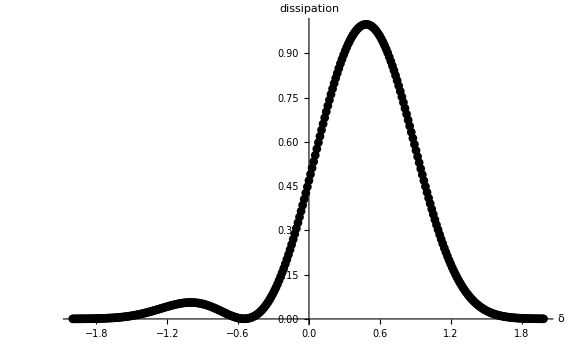

```mathematica
(*Isotropic dimensionless dissipation for X-wave; δ == χ^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ]*)
δDissipation={};
χ=30;β=0.4;η=0;
δbegining=-2;δend=2;δnstep=300;
ProgressIndicator[Dynamic[(δ-δbegining)/(δend-δbegining)]]
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,
δDissipation=Append[δDissipation,{δ,Impedance[10^-5,χ,(β*χ^(-2/3))^2,ArcSin[δ*χ^(-1/3)],η,{0,1}]⟦1⟧}];
];
Clear[χ,β,δ,η];

experiment=ListPlot[δDissipation,PlotRange->Full,AxesLabel->{δ,dissipation},LabelStyle->{FontSize->14},PlotStyle->Black, PlotMarkers->Automatic];
(*fittingFunction=Function[δ,a*δ^2 *Exp[-b*Abs[δ]^3 ]];
fit=FindFit[δDissipation,fittingFunction[δ],{a,b},δ];
theory=Plot[fittingFunction[δ]/.fit,{δ,δbegining,δend},PlotRange->Full(*,PlotLegends->ToString[fittingFunction[δ]/.fit,TraditionalForm]*)];*)

result=Show[{experiment(*,theory*)},ImageSize->Large]

(*SaveData["results/isotropism/isotropism.csv",δDissipation,"CSV"]
SaveData["results/isotropism/isotropism.png",result,"PNG"]*)
Clear[experiment,theory,fittingFunction,fit,result];
```

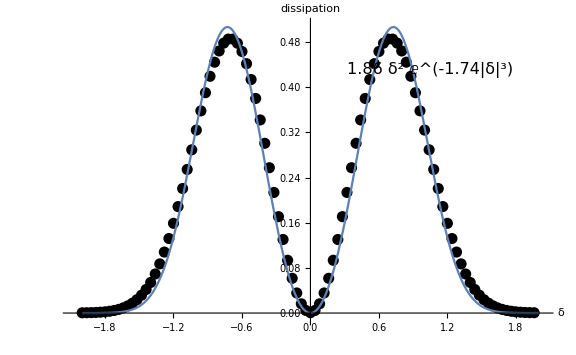

```mathematica
(*Anisotropic dimensionless dissipation for X-wave, η == 0; δ == χ^(1/3)Sin[θ] == (Subscript[k, 0] L)^(1/3)*Sin[θ], β == χ^(2/3)√u*)
δβDissipation={};
χ=30;
δbegining=-2;δend=2;δnstep=100;
βbegining =0; βend = 1.2; βnstep = 100;
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)+((βend-βbegining)/βnstep)*(δ-δbegining)/(δend-δbegining)]]
For[β=βbegining,β<βend,β+=(βend-βbegining)/βnstep,
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,
δβDissipation=Append[δβDissipation,{δ,β,Impedance[10^-5,χ,(β*χ^(-2/3))^2,ArcSin[δ*χ^(-1/3)],0,{0,1}]⟦1⟧}];
];
];
Clear[δ,β];

experiment=ListPlot3D[δβDissipation,PlotRange->Full,AxesLabel->{δ,β,dissipation}];
result=Show[{experiment},ImageSize->Large]

SaveData["results/eta/eta.csv",δβDissipation,"CSV"]
SaveData["results/eta/eta.png",result,"PNG"]

βδMinimum={};
βδMaximum={};
βMaxDissipation={};

βmax=0.5;n=0;
ProgressIndicator[Dynamic[(β-βbegining)/(βmax-βbegining)]]
For[β=βbegining,β<βmax,β+=(βend-βbegining)/βnstep,
δDissipation=Table[{δβDissipation⟦n*βnstep+i,1⟧,δβDissipation⟦n*βnstep+i,3⟧},{i,1,δnstep}];
interpolation=Interpolation[δDissipation];
δmin=x/.Last[FindMinimum[{interpolation[x],δbegining<x<δend},{x,0}]];
βδMinimum=Append[βδMinimum,{β,δmin}];
δmax=x/.Last[FindMaximum[{interpolation[x],δbegining<x<δend},{x,0.4}]];
βδMaximum=Append[βδMaximum,{β,δmax}];
maxDissipation=First[FindMaximum[{interpolation[x],δbegining<x<δend},{x,0.4}]];
βMaxDissipation = Append[βMaxDissipation,{β,maxDissipation}];
n+=1;
];
Clear[χ,δ,β,n];

experiment=ListPlot[βδMinimum,PlotRange->Full,AxesLabel->{β,δ},PlotStyle->Black];
fittingFunction=Function[β,a*β];
fit=FindFit[βδMinimum,fittingFunction[β],a,β];
theory=Plot[fittingFunction[β]/.fit,{β,βbegining,βmax},PlotRange->Full,PlotLegends->ToString[fittingFunction[β]/.fit,TraditionalForm]];

result=Show[{experiment,theory},ImageSize->Large]

SaveData["results/eta/zeroDissipationFromAnisortopism.csv",βδMinimum,"CSV"]
SaveData["results/eta/zeroDissipationFromAnisortopism.png",result,"PNG"]

experiment=ListPlot[βδMaximum,PlotRange->Full,AxesLabel->{β,δ},PlotStyle->Black];
fittingFunction=Function[β,a+b*β];
fit=FindFit[βδMaximum,fittingFunction[β],{a,b},β];
theory=Plot[fittingFunction[β]/.fit,{β,βbegining,βmax},PlotRange->Full,PlotLegends->ToString[fittingFunction[β]/.fit,TraditionalForm]];

result=Show[{experiment,theory},ImageSize->Large]

SaveData["results/eta/maxDissipationFromAnisortopism.csv",βδMaximum,"CSV"]
SaveData["results/eta/maxDissipationFromAnisortopism.png",result,"PNG"]

experiment=ListPlot[βMaxDissipation,PlotRange->Full,AxesLabel->{β,δ},PlotStyle->Black];

result=Show[{experiment},ImageSize->Large]

SaveData["results/eta/maxValueDissipationFromAnisortopism.csv",βMaxDissipation,"CSV"]
SaveData["results/eta/maxValueDissipationFromAnisortopism.png",result,"PNG"]
Clear[experiment,theory,fittingFunction,fit,result];
```

-Graphics3D-

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/eta.csv

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/eta.png

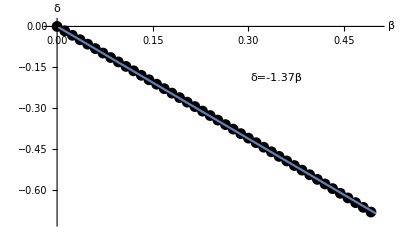

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/zeroDissipationFromAnisortopism.csv

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/zeroDissipationFromAnisortopism.png

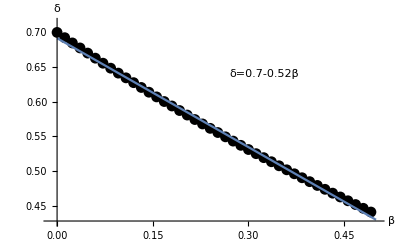

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/maxDissipationFromAnisortopism.csv

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/maxDissipationFromAnisortopism.png

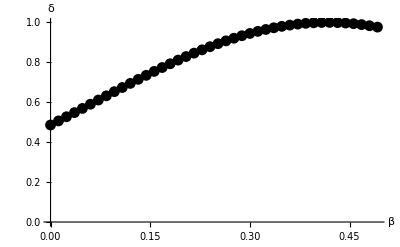

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/maxValueDissipationFromAnisortopism.csv

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/eta/maxValueDissipationFromAnisortopism.png

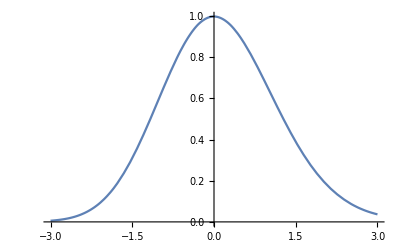

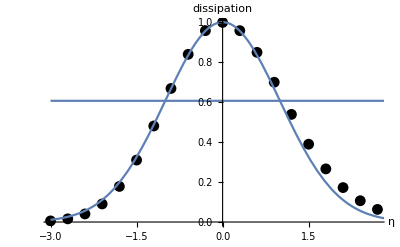

```mathematica
ηDissipation={};
σ=0.07;χ=30;υ=(2 √2 π χ σ^2)^-4;
ηbegining=ArcSin[√((√υ)/(1+√υ))]-3σ;ηend=ArcSin[√((√υ)/(1+√υ))]+3σ;ηnstep=20;
ProgressIndicator[Dynamic[(η-ηbegining)/(ηend-ηbegining)]]
For[η=ηbegining,η<ηend,η+=(ηend-ηbegining)/ηnstep,
AppendTo[ηDissipation,{(η-ArcSin[√((√υ)/(1+√υ))])/σ,Impedance[10^-5,χ,υ,0,η,{1,0}]⟦1⟧}];
];
Plot[Interpolation[ηDissipation][x],{x,-3,3}]
experiment=ListPlot[ηDissipation,PlotRange->Full,AxesLabel->{"η","dissipation"},PlotStyle->Black];
result=Show[{experiment,Plot[{ⅇ^(-1/2)},{x,-3,3}](*,theory*),Plot[ⅇ^(-ϕ^2/2),{ϕ,-3,3}]}]
Clear[σ,χ,υ,θ,η];
(*SaveData["results/isotropism/isotropism.csv",βDissipation,"CSV"]
SaveData["results/isotropism/isotropism.png",result,"PNG"]*)
Clear[experiment,theory,fittingFunction,fit,result];
```

```mathematica
(2 √2 π )^(-1/2)//N
```

0.335469

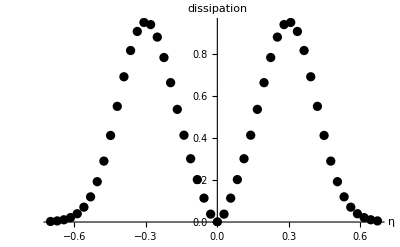

```mathematica
ηDissipation={};
υ=0.01;χ=30;
ηbegining=-0.7;ηend=0.7;ηnstep=50;
ProgressIndicator[Dynamic[(η-ηbegining)/(ηend-ηbegining)]]
For[η=ηbegining,η<ηend,η+=(ηend-ηbegining)/ηnstep,
ηDissipation=Append[ηDissipation,{η,Impedance[10^-5,χ,υ,0,η,{1,0}]⟦1⟧}];
];
Clear[σ,χ,υ,θ,η];

experiment=ListPlot[ηDissipation,PlotRange->Full,AxesLabel->{η,dissipation},PlotStyle->Black];
result=Show[{experiment(*,theory*)}]

(*SaveData["results/isotropism/isotropism.csv",βDissipation,"CSV"]
SaveData["results/isotropism/isotropism.png",result,"PNG"]*)
Clear[experiment,theory,fittingFunction,fit,result];
```

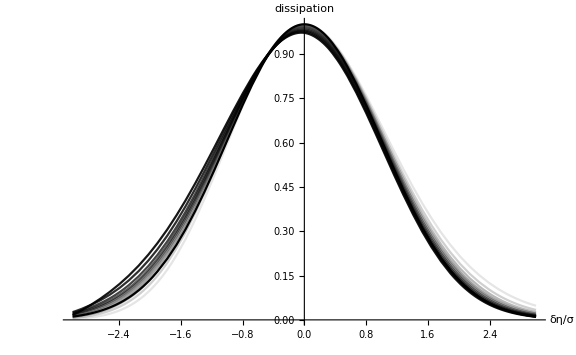

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/teta/teta.png

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/results/teta/teta.png

```mathematica
(*Anisotropic dimensionless dissipation for O-wave, θ == 0; σ == χSin[Subscript[η, 0]]^2 == χ(√u)/(1+√u)*)
ηχDissipation={};
σ=0.07;
χbegining=(2 √2 π σ^2)^-1+1;χend=(2 √2 π σ^2)^(-3/2)-1;χnstep=10;ηnstep = 20;
ProgressIndicator[Dynamic[(χ-χbegining)/(χend-χbegining)]]
For[χ=χbegining,χ<χend,χ+=(χend-χbegining)/χnstep,
υ=(2 √2 π χ σ^2)^-4;H=ArcSin[√((√υ)/(1+√υ))];ηbegining=H-3σ;ηend=H+3σ;
ηDissipation={};
For[η=ηbegining,η<ηend,η+=(ηend-ηbegining)/ηnstep,
AppendTo[ηDissipation,{(η-H)/σ,Impedance[10^-5,χ,υ,0,η,{1,0}]⟦1⟧}];
];
AppendTo[ηχDissipation,{χ,Interpolation[ηDissipation]}];
];

experiment=Plot[Evaluate@Table[ηχDissipation⟦i⟧⟦2⟧[x],{i,1,Length[ηχDissipation]}],{x,-3,3},PlotRange->Full,AxesLabel->{"δη/σ","dissipation"},LabelStyle->{FontSize->14},PlotStyle->Table[RGBColor[0,0,0,i],{i,0.1,1,0.9/Length[ηχDissipation]}]];
theory=Plot[ⅇ^(-x^2/2),{x,-3,3},PlotStyle->{Black},PlotLegends->"Expressions"];
result=Show[{experiment,theory},ImageSize->Large]
Clear[χ,σ,η,H,υ,experiment,theory,result];

(*SaveData["results/teta/teta.csv",ησDissipation,"CSV"]*)
SaveData["results/teta/teta.png",result,"PNG"]
```

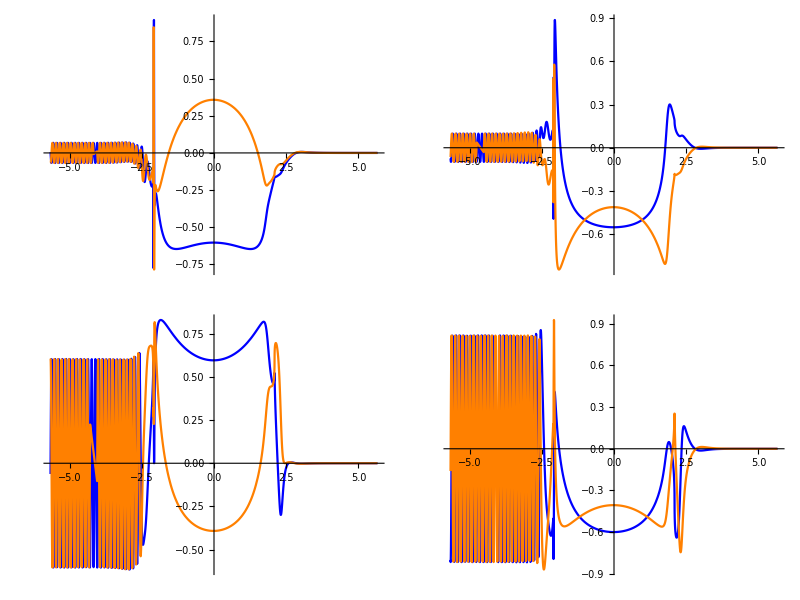
{0.00280604,(-Graphics-)}

```mathematica
χ=30;υ=0.1;η=0.5;θ=0;(*ArcSin[√((√υ)/(1+√υ))]*)
Impedance[10^-5,χ,υ,θ,η,{0,1}];
{%⟦1⟧,Table[Plot[{Re[%⟦2⟧⟦i,j⟧],Im[%⟦2⟧⟦i,j⟧]},{x,-2%⟦3⟧,2%⟦3⟧},ImageSize->Medium,PlotRange->Full,PlotStyle->{Blue,Orange,Black}],{i,1,2},{j,1,2}]//MatrixForm}
Clear[χ,υ,θ,η]
```